1 | {0,0,0,0} | {{1→1,True}}
2 | {0,0,0,1} | {{2→1,d+r<1+d p},{2→2,d+r>1+d p}}
3 | {0,0,1,0} | {{3→1,True}}
4 | {0,0,1,1} | {{4→1,True}}
5 | {0,1,0,0} | {{5→1,d<p+d p},{5→14,d>p+d p}}
6 | {0,1,0,1} | {{6→1,(p+r<1&&d<p+d p)||(p+r≥1&&d+r<1+d p)},{6→4,p+r>1&&(-1+r)/(-1+p)<d<p/r},{6→13,p+r<1&&d>p+d p&&r+d r<1},{6→16,(p+r≤1&&r+d r>1)||(p+r>1&&d r>p)}}
7 | {0,1,1,0} | {{7→1,d<p},{7→10,d>p}}
8 | {0,1,1,1} | {{8→1,d<p},{8→9,d>p}}
9 | {1,0,0,0} | {{9→1,True}}
10 | {1,0,0,1} | {{10→1,(1+d) r<1+d p},{10→10,(1+d) r>1+d p}}
11 | {1,0,1,0} | {{11→1,True}}
12 | {1,0,1,1} | {{12→1,True}}
13 | {1,1,0,0} | {{13→1,True}}
14 | {1,1,0,1} | {{14→1,(1+d) r<1+d p},{14→12,(1+d) r>1+d p}}
15 | {1,1,1,0} | {{15→1,True}}
16 | {1,1,1,1} | {{16→1,True}}

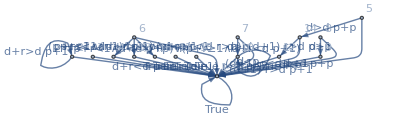

```mathematica
result[i_, strats_]:=
Module[{input = i, str = strats},
output = {};
transpoints = {};
Do[{
strat = str[[j]];
assumptions = {
               If[strat[[1]]==0, Q1000>Q1001, Q1000<Q1001],
               If[strat[[2]]==0, Q1010>Q1011, Q1010<Q1011],
               If[strat[[3]]==0, Q1100>Q1101, Q1100<Q1101],
               If[strat[[4]]==0, Q1110>Q1111, Q1110<Q1111],
               If[input[[1]]==0, Q2000>Q2001, Q2000<Q2001],
               If[input[[2]]==0, Q2100>Q2101, Q2100<Q2101],
               If[input[[3]]==0, Q2010>Q2011, Q2010<Q2011],
               If[input[[4]]==0, Q2110>Q2111, Q2110<Q2111],
               ,t>r>p>s,2r>t+s,,t==1,s==0, 0<d<1};

Assuming[assumptions,
{q1 = Simplify[Boole[Q2000>Q2001] (p+d*Q1000*Boole[Q1000>Q1001]+d*Q1001*Boole[Q1000<Q1001])+
                        Boole[Q2000<Q2001] (t+d*Q1010*Boole[Q1010>Q1011]+d*Q1011*Boole[Q1010<Q1011])],
q2=  Simplify[Boole[Q2000>Q2001] (s+d*Q1100*Boole[Q1100>Q1101]+d*Q1101*Boole[Q1100<Q1101])+
                        Boole[Q2000<Q2001] (r+d*Q1110*Boole[Q1110>Q1111]+d*Q1111*Boole[Q1110<Q1111])],
q3=  Simplify[Boole[Q2010>Q2011] (p+d*Q1000*Boole[Q1000>Q1001]+d*Q1001*Boole[Q1000<Q1001])+
                        Boole[Q2010<Q2011] (t+d*Q1010*Boole[Q1010>Q1011]+d*Q1011*Boole[Q1010<Q1011])],
q4=  Simplify[Boole[Q2010>Q2011] (s+d*Q1100*Boole[Q1100>Q1101]+d*Q1101*Boole[Q1100<Q1101])+
                        Boole[Q2010<Q2011] (r+d*Q1110*Boole[Q1110>Q1111]+d*Q1111*Boole[Q1110<Q1111])],
q5=  Simplify[Boole[Q2100>Q2101] (p+d*Q1000*Boole[Q1000>Q1001]+d*Q1001*Boole[Q1000<Q1001])+
                        Boole[Q2100<Q2101] (t+d*Q1010*Boole[Q1010>Q1011]+d*Q1011*Boole[Q1010<Q1011])],
q6=  Simplify[Boole[Q2100>Q2101] (s+d*Q1100*Boole[Q1100>Q1101]+d*Q1101*Boole[Q1100<Q1101])+
                        Boole[Q2100<Q2101] (r+d*Q1110*Boole[Q1110>Q1111]+d*Q1111*Boole[Q1110<Q1111])],
q7=  Simplify[Boole[Q2110>Q2111] (p+d*Q1000*Boole[Q1000>Q1001]+d*Q1001*Boole[Q1000<Q1001])+
                         Boole[Q2110<Q2111] (t+d*Q1010*Boole[Q1010>Q1011]+d*Q1011*Boole[Q1010<Q1011])],
q8=  Simplify[Boole[Q2110>Q2111] (s+d*Q1100*Boole[Q1100>Q1101]+d*Q1101*Boole[Q1100<Q1101])+
                         Boole[Q2110<Q2111] (r+d*Q1110*Boole[Q1110>Q1111]+d*Q1111*Boole[Q1110<Q1111])]
}];
sol1=Solve[{q1==Q1000, q2==Q1001, q3==Q1010, q4==Q1011, q5==Q1100, q6==Q1101, q7==Q1110, q8==Q1111},{Q1000, Q1001, Q1010, Q1011, Q1100, Q1101, Q1110, Q1111}];
formula1 = Simplify[Assuming[assumptions,
 Simplify[Reduce[
  If[strat[[1]]==0,Simplify[sol1[[1]][[1]][[2]] > sol1[[1]][[2]][[2]]], Simplify[sol1[[1]][[1]][[2]] < sol1[[1]][[2]][[2]]]] && 
If[strat[[2]]==0,Simplify[sol1[[1]][[3]][[2]] > sol1[[1]][[4]][[2]]], Simplify[sol1[[1]][[3]][[2]] < sol1[[1]][[4]][[2]]]] && 
If[strat[[3]]==0,Simplify[sol1[[1]][[5]][[2]] > sol1[[1]][[6]][[2]]], Simplify[sol1[[1]][[5]][[2]] < sol1[[1]][[6]][[2]]]] && 
If[strat[[4]]==0,Simplify[sol1[[1]][[7]][[2]] > sol1[[1]][[8]][[2]]], Simplify[sol1[[1]][[7]][[2]] < sol1[[1]][[8]][[2]]]],d,Reals]]]];
If[(formula1 === False)==False , AppendTo[output,{FromDigits[i,2]+1->j,Simplify[formula1]}]];
},{j,1,16}];
output
];

strats = {};
Do[AppendTo[strats, Join[ConstantArray[0,4-Length[IntegerDigits[i,2]]],IntegerDigits[i,2]]],{i,0,15}];


transitions = {};
Do[AppendTo[transitions,result[strats[[i]],strats]],{i,1,16}];

grid = {};
Do[AppendTo[grid,{FromDigits[strats[[i]],2]+1, strats[[i]],transitions[[i]]}],{i,1,16}]
Grid[grid,Frame->All]

edges = {};
Do[Do[AppendTo[edges, transitions[[i]][[j]][[1]]],{j,1,Length[transitions[[i]]]}],{i,1,Length[transitions]}];

labels = {};
Do[Do[AppendTo[labels, transitions[[i]][[j]][[1]] -> transitions[[i]][[j]][[2]]],{j,1,Length[transitions[[i]]]}],{i,1,Length[transitions]}];

GraphPlot[edges, VertexLabels->Automatic,  DirectedEdges->True,EdgeLabels->labels, ImageSize->Full]
```

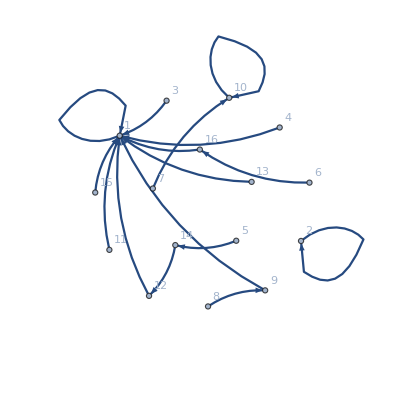

```mathematica
weights = Import["/home/lars/Documents/Year 3/Bachelor project/Informatica/Python/network.csv"];
Do[weights[[i]]=Normalize[weights[[i]],Total],{i,1,16}];
weights= Flatten[weights];

edges = {};
Do[Do[AppendTo[edges,i->j],{j,1,16}],{i,1,16}]; 
Graph[edges,EdgeStyle->Thread[edges->Thread@{(Opacity[#]&/@weights),(Thickness[#/250]&/@weights)}],ImageSize->Full,VertexLabels->Automatic]
```